Macro for exported figures to file.

```mathematica
$doExport=True;
exportme[name_][fig_]:=(SetDirectory[NotebookDirectory[]];if[$doExport,Export["../fig/"<>name<>".pdf",fig];Export["../fig/"<>name<>".png",fig]];fig)
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

#### Moments

In this section we compute the moments of a system drifting according to two Ornstein-Uhlenbeck processes.

```mathematica
$Assumptions=σν>0&&θν>0&&0<Γ<α1&&0<κ0<1&&σκ>0&&θκ>0&&t>0;
```

```mathematica
p[expr_]:=TransformedProcess[
expr,
{
ν\[Distributed]OrnsteinUhlenbeckProcess[0,σν,θν,α1-Γ],
κ\[Distributed]OrnsteinUhlenbeckProcess[κ0,σκ,θκ]
},
t
]
```

```mathematica
αmean1=p[Γ+ν[t]][t]//Mean
βmean1=p[Γ+κ[t]ν[t]][t]//Mean
αvar1=p[Γ+ν[t]][t]//Variance
βvar1=p[Γ+κ[t]ν[t]][t]//Variance//Expand
αβproduct=(Γ+ν[t])(Γ+κ[t]ν[t])//Expand;
(*We need to compute the covariance manually using Cov[a,b]=Mean[a*b]-Mean[a]Mean[b]*)
αβcov1=Sum[Mean[p[expr][t]],{expr,List@@αβproduct}]-αmean*βmean//Expand
```

ⅇ^(-t θν) (α1-Γ)+Γ

ⅇ^(-t θν) (ⅇ^(t θν) Γ+(α1-Γ) κ0)

((1-ⅇ^(-2 t θν)) σν^2)/(2 θν)

(ⅇ^(-2 t θν) α1^2 σκ^2)/(2 θκ)-(ⅇ^(-2 t θν) α1 Γ σκ^2)/θκ+(ⅇ^(-2 t θν) Γ^2 σκ^2)/(2 θκ)+(κ0^2 σν^2)/(2 θν)-(ⅇ^(-2 t θν) κ0^2 σν^2)/(2 θν)+(σκ^2 σν^2)/(4 θκ θν)-(ⅇ^(-2 t θν) σκ^2 σν^2)/(4 θκ θν)

-αmean βmean+ⅇ^(-t θν) α1 Γ+Γ^2-ⅇ^(-t θν) Γ^2+ⅇ^(-2 t θν) α1^2 κ0-2 ⅇ^(-2 t θν) α1 Γ κ0+ⅇ^(-t θν) α1 Γ κ0+ⅇ^(-2 t θν) Γ^2 κ0-ⅇ^(-t θν) Γ^2 κ0+(κ0 σν^2)/(2 θν)-(ⅇ^(-2 t θν) κ0 σν^2)/(2 θν)

```mathematica
totalExp[mean_]:=Mean[TransformedDistribution[mean,α1\[Distributed]NormalDistribution[α0,σα]]]
totalVar[mean_,var_]:=Variance[TransformedDistribution[mean,α1\[Distributed]NormalDistribution[α0,σα]]]+Mean[TransformedDistribution[var,α1\[Distributed]NormalDistribution[α0,σα]]]
totalCov[mean1_,mean2_,cov_]:=Covariance[TransformedDistribution[{mean1,mean2},α1\[Distributed]NormalDistribution[α0,σα]],1,2]+Mean[TransformedDistribution[cov,α1\[Distributed]NormalDistribution[α0,σα]]]
```

```mathematica
αmean=totalExp[αmean1]
βmean=totalExp[βmean1]
αvar=totalVar[αmean1,αvar1]
βvar=totalVar[βmean1,βvar1]//Expand
αβcov=totalCov[αmean1,βmean1,αβcov1]
```

ⅇ^(-t θν) (α0+(-1+ⅇ^(t θν)) Γ)

Γ+ⅇ^(-t θν) α0 κ0-ⅇ^(-t θν) Γ κ0

ⅇ^(-2 t θν) σα^2+((1-ⅇ^(-2 t θν)) σν^2)/(2 θν)

ⅇ^(-2 t θν) κ0^2 σα^2+(ⅇ^(-2 t θν) α0^2 σκ^2)/(2 θκ)-(ⅇ^(-2 t θν) α0 Γ σκ^2)/θκ+(ⅇ^(-2 t θν) Γ^2 σκ^2)/(2 θκ)+(ⅇ^(-2 t θν) σα^2 σκ^2)/(2 θκ)+(κ0^2 σν^2)/(2 θν)-(ⅇ^(-2 t θν) κ0^2 σν^2)/(2 θν)+(σκ^2 σν^2)/(4 θκ θν)-(ⅇ^(-2 t θν) σκ^2 σν^2)/(4 θκ θν)

ⅇ^(-2 t θν) κ0 σα^2+(ⅇ^(-2 t θν) κ0 (2 θν σα^2-σν^2+ⅇ^(2 t θν) σν^2))/(2 θν)

#### Numerics

In this section we simulate a trajectory of the model and compare it to the moment formulas.

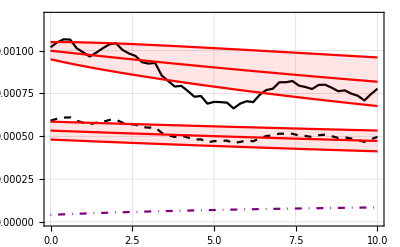

```mathematica
reps={σν->0.00005,θν->0.03,α1->1.02 10^-3,α0->10^-3,σα->0.5 10^-4,Γ->0.3 10^-3,κ0->1/3,σκ->0.01,θκ->0.01};
plt1=Plot[{αmean/.reps,(αmean+Sqrt[αvar])/.reps,(αmean-Sqrt[αvar])/.reps},{t,0,10},PlotRange->{0,Automatic},Filling->{2->{3}},PlotStyle->{{Red,Thin},{Red,Thin},{Red,Thin}}];
plt2=Plot[{βmean/.reps,(βmean+Sqrt[βvar])/.reps,(βmean-Sqrt[βvar])/.reps},{t,0,10},PlotRange->{0,Automatic},Filling->{2->{3}},PlotStyle->{{Red,Thin},{Red,Thin},{Red,Thin}}];
plt12=Plot[{αmean/.reps,(αmean+Sqrt[αvar])/.reps,(αmean-Sqrt[αvar])/.reps,βmean/.reps,(βmean+Sqrt[βvar])/.reps,(βmean-Sqrt[βvar])/.reps},{t,0,10},PlotRange->{0,Automatic},Filling->{2->{{3},Directive[Red,Opacity[0.1]]},5->{{6},Directive[Red,Opacity[0.1]]}},PlotStyle->{{Red,Thin},{Red,Thin},{Red,Thin}}];
plt4=Plot[{Sqrt[αβcov/.reps]},{t,0,10},PlotStyle->{Thick,Purple,DotDashed}];
plt3=ListPlot[RandomFunction[Evaluate[p[{Γ+ν[t],Γ+κ[t]ν[t],-1000}]/.reps],{0,10,0.2}],
PlotStyle->{{Black,Thick},{Black,Thick,Dashed},{Thick,Purple,DotDashed}},
Joined->True,
PlotTheme->"Detailed",
PlotRange->{0,1.2 10^-3},
FrameLabel->(MaTeX[#,FontSize->14]&/@{"\\text{time}","\\text{references}"}),
BaseStyle->texStyle,
PlotLegends->LineLegend[MaTeX[{"\\alpha(t)","\\beta(t)","\\sigma_{\\alpha\\beta}"},FontSize->14]]
];
fig1=exportme["stoch-variate"]@Show[{plt3,plt4,plt12}]
```